```mathematica
SetDirectory[NotebookDirectory[]];
```

## Plot potentials

### mD = 0.2 GeV, T = 0.155 GeV

```mathematica
αcont=SetPrecision[{0.5146004500017507,0.002579680095957094},20];(*10k run*)
σcont=SetPrecision[{0.16904257426266697,0.0009046347484072015},20];
ccont=SetPrecision[{-0.15782092474161866,0.0024785523617348124},20];
```

```mathematica
ReVsu10=Interpolation[ToExpression[Import["vel_pot/ReVsu10.dat"]]];
ReVsu20=Interpolation[ToExpression[Import["vel_pot/ReVsu20.dat"]]];
ReVsu30=Interpolation[ToExpression[Import["vel_pot/ReVsu30.dat"]]];
ReVsu40=Interpolation[ToExpression[Import["vel_pot/ReVsu40.dat"]]];
ReVsu50=Interpolation[ToExpression[Import["vel_pot/ReVsu50.dat"]]];
ReVsu60=Interpolation[ToExpression[Import["vel_pot/ReVsu60.dat"]]];
ReVsu70=Interpolation[ToExpression[Import["vel_pot/ReVsu70.dat"]]];
ReVsu80=Interpolation[ToExpression[Import["vel_pot/ReVsu80.dat"]]];
```

```mathematica
ReVcu10=Interpolation[ToExpression[Import["vel_pot/ReVcu10.dat"]]];
ReVcu20=Interpolation[ToExpression[Import["vel_pot/ReVcu20.dat"]]];
ReVcu30=Interpolation[ToExpression[Import["vel_pot/ReVcu30.dat"]]];
ReVcu40=Interpolation[ToExpression[Import["vel_pot/ReVcu40.dat"]]];
ReVcu50=Interpolation[ToExpression[Import["vel_pot/ReVcu50.dat"]]];
ReVcu60=Interpolation[ToExpression[Import["vel_pot/ReVcu60.dat"]]];
ReVcu70=Interpolation[ToExpression[Import["vel_pot/ReVcu70.dat"]]];
ReVcu80=Interpolation[ToExpression[Import["vel_pot/ReVcu80.dat"]]];
```

```mathematica
ImVcu10=Interpolation[ToExpression[Import["vel_pot/ImVcu10.dat"]]];
ImVcu20=Interpolation[ToExpression[Import["vel_pot/ImVcu20.dat"]]];
ImVcu30=Interpolation[ToExpression[Import["vel_pot/ImVcu30.dat"]]];
ImVcu40=Interpolation[ToExpression[Import["vel_pot/ImVcu40.dat"]]];
ImVcu50=Interpolation[ToExpression[Import["vel_pot/ImVcu50.dat"]]];
ImVcu60=Interpolation[ToExpression[Import["vel_pot/ImVcu60.dat"]]];
ImVcu70=Interpolation[ToExpression[Import["vel_pot/ImVcu70.dat"]]];
ImVcu80=Interpolation[ToExpression[Import["vel_pot/ImVcu80.dat"]]];
```

```mathematica
ImVsu10=Interpolation[ToExpression[Import["vel_pot/ImVsu10.dat"]]];
ImVsu20=Interpolation[ToExpression[Import["vel_pot/ImVsu20.dat"]]];
ImVsu30=Interpolation[ToExpression[Import["vel_pot/ImVsu30.dat"]]];
ImVsu40=Interpolation[ToExpression[Import["vel_pot/ImVsu40.dat"]]];
ImVsu50=Interpolation[ToExpression[Import["vel_pot/ImVsu50.dat"]]];
ImVsu60=Interpolation[ToExpression[Import["vel_pot/ImVsu60.dat"]]];
ImVsu70=Interpolation[ToExpression[Import["vel_pot/ImVsu70.dat"]]];
ImVsu80=Interpolation[ToExpression[Import["vel_pot/ImVsu80.dat"]]];
```

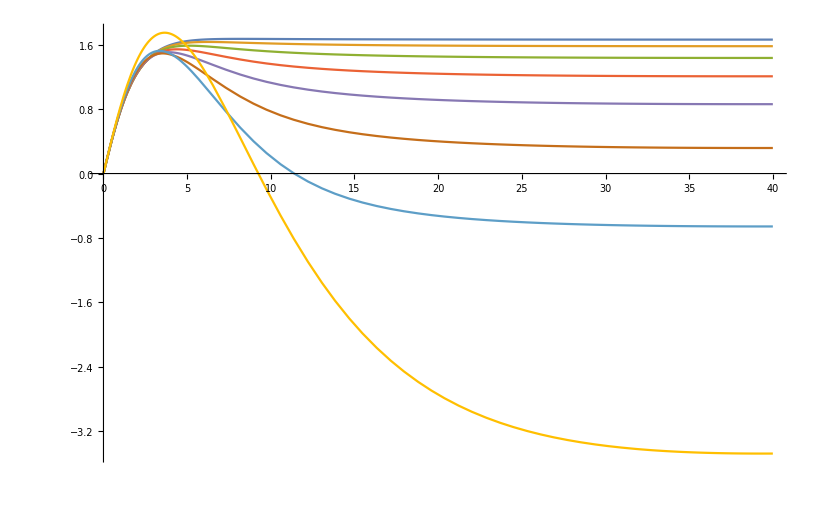

```mathematica
Plot[{ReVsu10[r/0.197],ReVsu20[r/0.197],ReVsu30[r/0.197],ReVsu40[r/0.197],ReVsu50[r/0.197],ReVsu60[r/0.197],ReVsu70[r/0.197],ReVsu80[r/0.197]},{r,0,40},PlotRange->All]
```

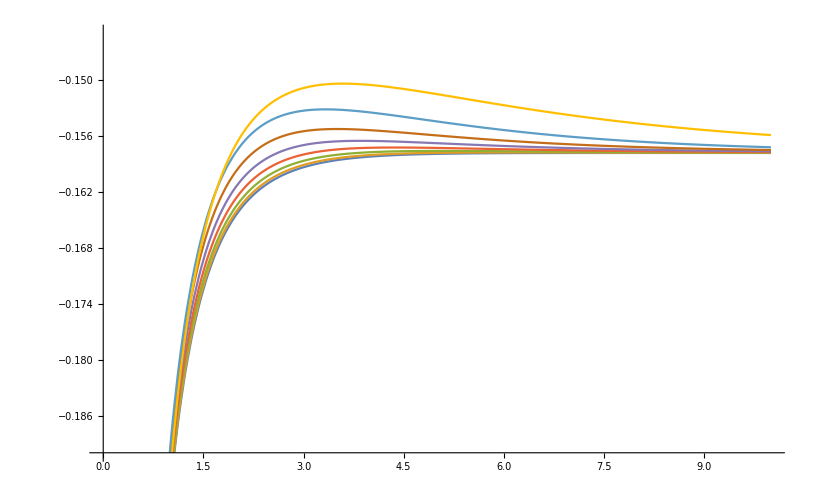

```mathematica
Plot[{ReVcu10[r/0.197],ReVcu20[r/0.197],ReVcu30[r/0.197],ReVcu40[r/0.197],ReVcu50[r/0.197],ReVcu60[r/0.197],ReVcu70[r/0.197],ReVcu80[r/0.197]},{r,0,10},PlotRange->{-0.19,-0.145}]
```

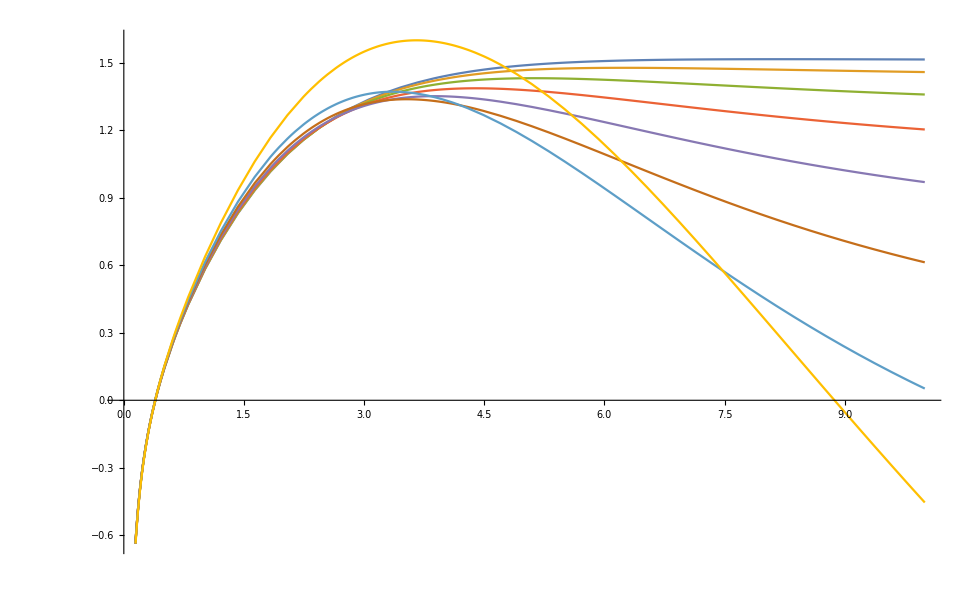

```mathematica
Plot[{ReVsu10[r/0.197]+ReVcu10[r/0.197],ReVcu20[r/0.197]+ReVsu20[r/0.197],ReVsu30[r/0.197]+ReVcu30[r/0.197],ReVsu40[r/0.197]+ReVcu40[r/0.197],ReVsu50[r/0.197]+ReVcu50[r/0.197],ReVsu60[r/0.197]+ReVcu60[r/0.197],ReVsu70[r/0.197]+ReVcu70[r/0.197],ReVsu80[r/0.197]+ReVcu80[r/0.197]},{r,0,10}]
```

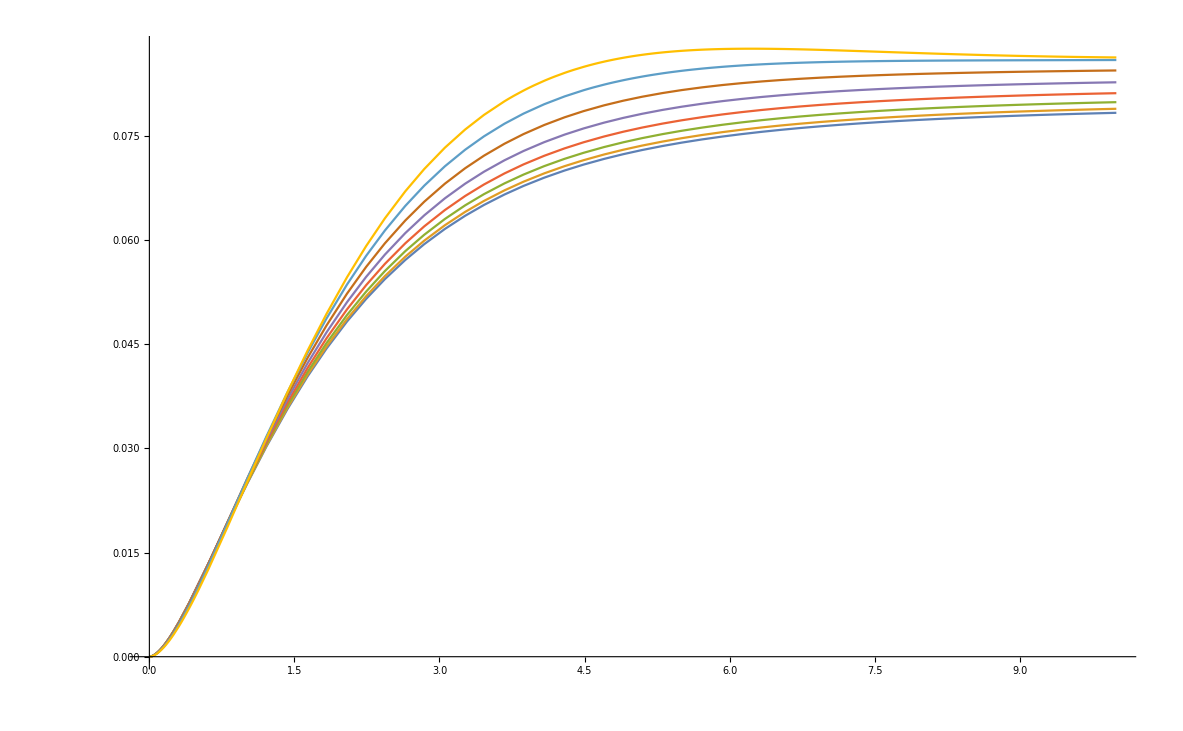

```mathematica
Plot[{Re[ImVcu10[r/0.197]],Re[ImVcu20[r/0.197]],Re[ImVcu30[r/0.197]],Re[ImVcu40[r/0.197]],Re[ImVcu50[r/0.197]],Re[ImVcu60[r/0.197]],Re[ImVcu70[r/0.197]],Re[ImVcu80[r/0.197]]},{r,1/1000,10},PlotRange->All]
```

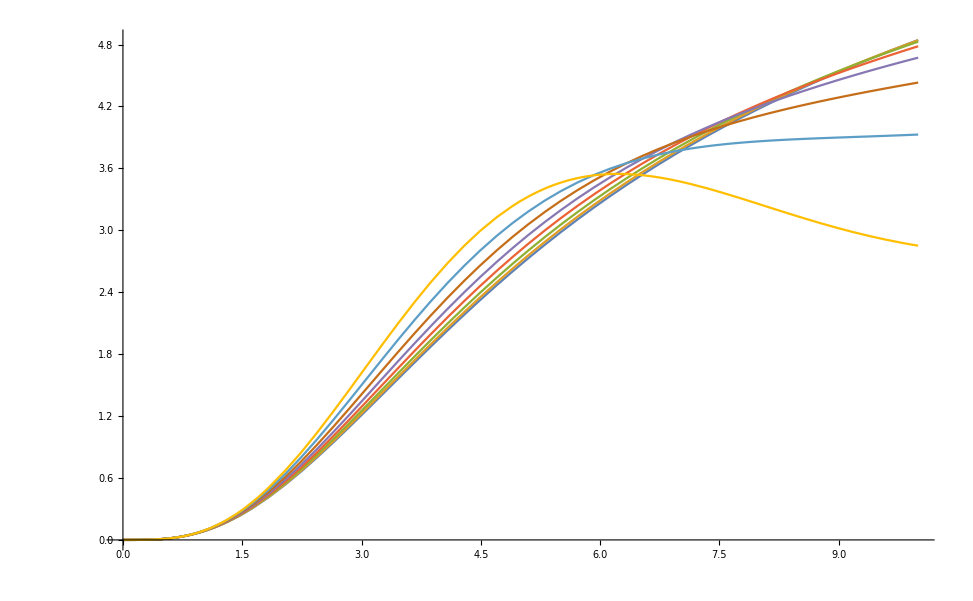

```mathematica
Plot[{ImVsu10[r/0.197],ImVsu20[r/0.197],ImVsu30[r/0.197],ImVsu40[r/0.197],ImVsu50[r/0.197],ImVsu60[r/0.197],ImVsu70[r/0.197],ImVsu80[r/0.197]},{r,0,10},PlotRange->All]
```

```mathematica
Πpar[θ_,mD_,u_]:=mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))]);
```

```mathematica
ReVcpp[r_,mD_,u_,α_,c_]:=Re[c-α/r+α NIntegrate[Sin[θ] √Πpar[θ,mD,u] Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];
ReVspp[r_,mD_,u_,σ_]:=Re[σ/2 NIntegrate[Sin[θ] 1/(√Πpar[θ,mD,u])Exp[-√Πpar[θ,mD,u]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20]];
```

```mathematica
ReVcp[r_,mD_,u_,α_,c_]:=c-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,mD,u]] Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];
ReVsp[r_,mD_,u_,σ_]:=σ/2 NIntegrate[Sin[θ] 1/(√Re[Πpar[θ,mD,u]])Exp[-√Re[Πpar[θ,mD,u]]r Cos[θ]],{θ,0,π/2},MaxRecursion->20,WorkingPrecision->20];
```

```mathematica
ReVcu01=Interpolation[ParallelTable[{r,ReVcp[r,2/10,1/1000,αcont[[1]],ccont[[1]]]},{r,1/1000,200,1/100}]];
```

```mathematica
ReVsu80=Interpolation[ParallelTable[{r,ReVspp[r,2/10,8/10,σcont[[1]]]},{r,1/1000,200,1/100}]];
```

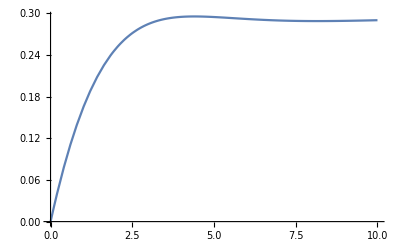

```mathematica
Plot[-ReVsu80[r/0.197]+ReVsu80[1/100],{r,0,10},PlotRange->All]
```

```mathematica
ReVsu80=Interpolation[ParallelTable[{r,ReVsp[r,2/10,8/10,σcont[[1]]]},{r,1/1000,200,1/100}]];
```

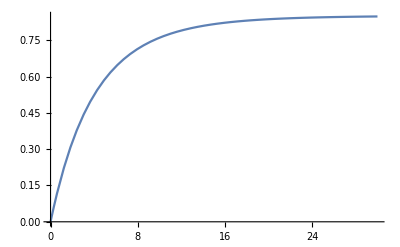

```mathematica
Plot[-ReVsu80[r/0.197]+ReVsu80[1/100],{r,0,30},PlotRange->All]
```